-1.19866+0.229693 (-2.5+t)+2.68097 (-2.5+t)^2

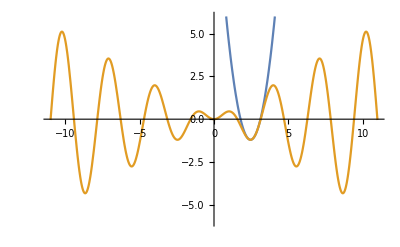

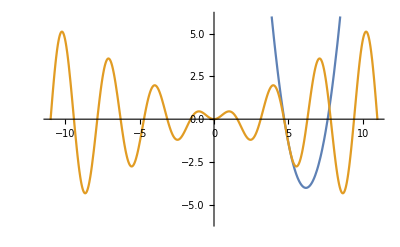

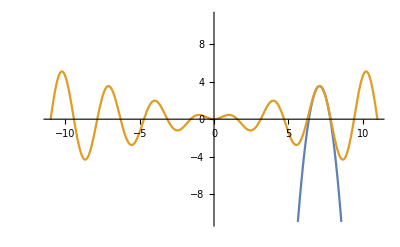

```mathematica
f[y_] := (
Return [y*Sin[y]*Cos[y]];
);

T[g_,x0_] := (
Return [g[x0] + g'[x0]*(t-x0) + (g''[x0]*(t-x0)^2)/2!];
);
Print[T[f,2.5]];
T1 = T[f,2.5];
T2 = T[f,5];
T3 = T[f,7];
Plot[{T1/.{t->x},f[x]},{x,-11,11},PlotRange->{{-11,11},{-6,6}}]
Plot[{T2/.{t->x},f[x]},{x,-11,11},PlotRange->{{-11,11},{-6,6}}]
Plot[{T3/.{t->x},f[x]},{x,-11,11},PlotRange->{{-11,11},{-11,11}}]
```

```mathematica
□_□
```

□_□

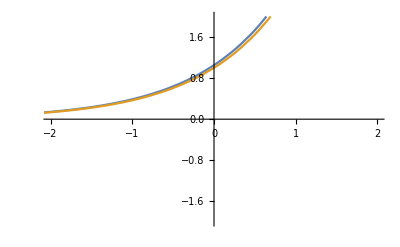

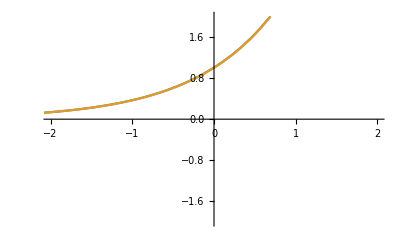

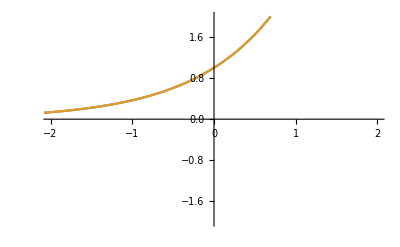

1.05171

0.454649

```mathematica
f1[z_] := E^z;
R[t_,h_] := Return[(f1[t+h]-f1[t])/h];
Plot[{R[x,0.1],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,0.01],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,(10^(-12))],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
N[R[0,0.1]]
```

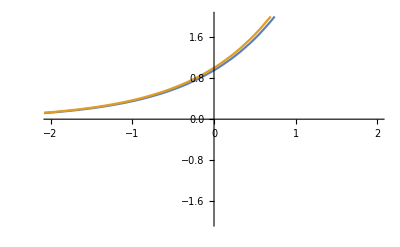

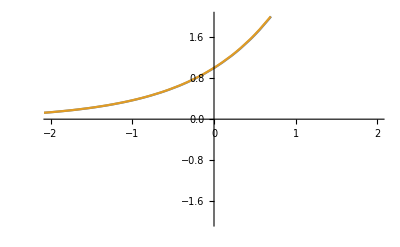

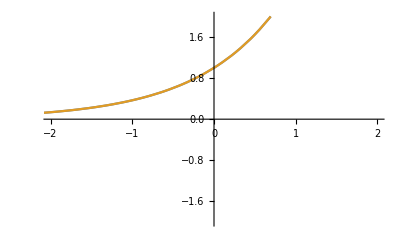

0.951626

```mathematica
f1[z_] := E^z;
R[t_,h_] := Return[(f1[t]-f1[t-h])/h];
Plot[{R[x,0.1],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,0.01],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,0.001],f1[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
N[R[0,0.1]]
```

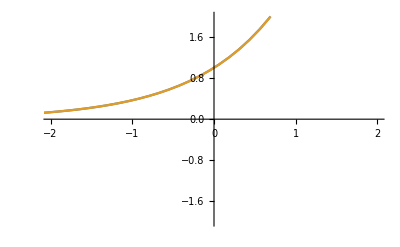

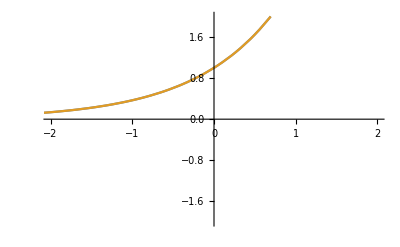

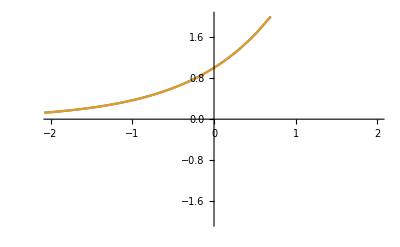

1.00167

```mathematica
f1[z_] := E^z;
R[t_,h_] := Return[(f1[t+h]-f1[t-h])/(2*h)];
Plot[{R[x,0.1],f1'[x]},{x,-3,3},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,0.01],f1'[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
Plot[{R[x,0.001],f1'[x]},{x,-11,11},PlotRange->{{-2,2},{-2,2}}]
N[R[0,0.1]]
```

1.00167

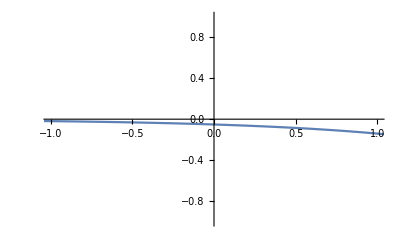

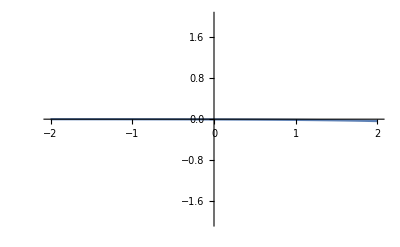

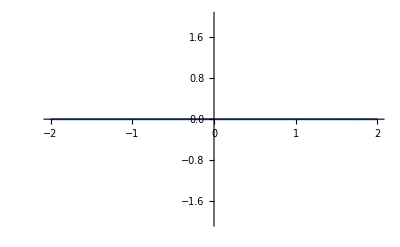

1.05171

```mathematica
1.001667500198441
(*Absolute error calculation for forward*)
f1[z_] := E^z;
R[t_,h_] := Return[(f1[t+h]-f1[t])/h];
Plot[{-(R[x,0.1]-f1[x])},{x,-5,5},PlotRange->{{-1,1},{-1,1}}]
Plot[{-(R[x,0.01]-f1[x])},{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
Plot[{-(R[x,(10^(-12))]-f1[x])},{x,-2,2},PlotRange->{{-2,2},{-2,2}}]
N[R[0,0.1]]
```

```mathematica
.
```

```mathematica
(*Absolute error calculation for central*)
```

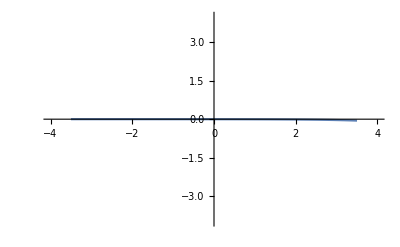

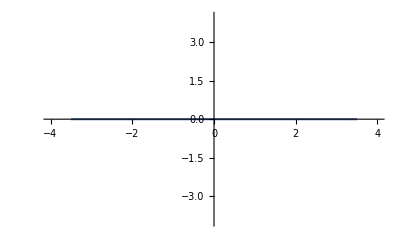

1.00167

```mathematica
f1[z_] := E^z;
R[t_,h_] := Return[(f1[t+h]-f1[t-h])/(2*h)];
Plot[{-(R[x,0.1]-f1'[x])},{x,-3.5,3.5},PlotRange->{{-4,4},{-4,4}}]
Plot[{-(R[x,0.01]-f1'[x])},{x,-3.5,3.5},PlotRange->{{-4,4},{-4,4}}]
N[R[0,0.1]]
```

```mathematica
solve(x^2+1 = 0)
```

Set::write: Tag Plus in 1+x^2 is Protected.

0

```mathematica
u[t_] := (0.01)/(0.01+0.99*E^(-10t));
```

{}

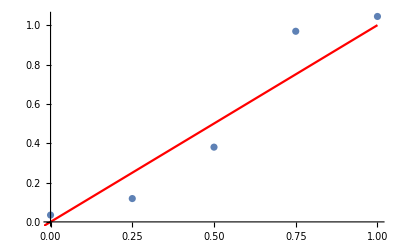

{}

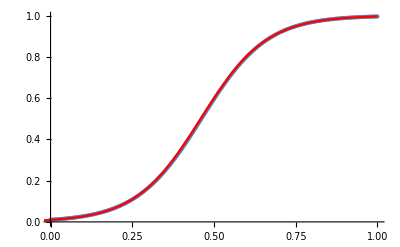

```mathematica
prev = 0.01;
h = 1/4;
arr4={};
arr50 = {};
arr250 = {}
For[i = 1,(i-1)*h<=1, ++i,
cur = prev + h*(10*prev*(1-prev));
AppendTo[arr4,{(i-1)*h,cur}];
prev = cur;
];
plot = ListPlot[arr4];
Show[plot,Plot[u,{u,-1,1},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}}]]

prev = 0.01;
h = 1/250;
arr4={};
arr50 = {};
arr250 = {}
For[i = 1,(i-1)*h<=1, ++i,
cur = prev + h*(10*prev*(1-prev));
AppendTo[arr250,{(i-1)*h,cur}];
prev = cur;
];
plot = ListPlot[arr250];
Show[plot,Plot[u[t],{t,-1,1},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}}]]
```